Model from the 2003 paper “EFFECTS OF FIRE AND HERBIVORY ON THE STABILITY OF SAVANNA ECOSYSTEMS”
Scenario B: mid water influx, water_in=500

Define parameters:

```mathematica
u=0.6;
rh=1.0;
rw=0.5;
dh=0.9;
dw=0.4;
alpha=0.4;
beta=300;
p=1;
```

Define water recharge rates:

```mathematica
win=500;
ws=alpha*(win-beta);

wt= win-ws;
```

Define system without fire effects

```mathematica
dhdt[H_,W_]:=rh*wt*(H)/(H+u*W+p*ws)-dh*H
```

```mathematica
dwdt[H_,W_]:=rw*((wt*u*W)/(H+u*W+p*ws)+ws)-dw*W
```

Find Fixed points

```mathematica
Simplify[Solve[dhdt[H,W]==0,H]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.},{H→386.667-0.6 W}}

^^Clearly H=386.66, W=0 solves dhdt=0.

```mathematica
p1=Plot[386.6666666666667-0.6*W,{W,0,750}];
```

```mathematica
Simplify[Solve[dwdt[H,W]==0,H]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→(8000.+295. W-0.6 W^2)/(-100.+W)}}

But apparently, it doesn’t think that W=0 is a solution because that requires rw*ws=0

```mathematica
p2=Plot[(8000.000000000002+295.00000000000006* W-0.6000000000000001* W^2)/(-100.+W),{W,0,750},PlotStyle->Red];
```

```mathematica
fp=Simplify[Solve[dwdt[H,W]==0 && dhdt[H,W]==0,{H,W}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.,W→-25.7681},{H→202.051,W→307.692},{H→0.,W→517.435}}

```mathematica
fp1=Part[fp,1]
```

{H→0.,W→-25.7681}

```mathematica
fp2=Part[fp,2]
```

{H→202.051,W→307.692}

```mathematica
fp3=Part[fp,3]
```

{H→0.,W→517.435}

```mathematica
p1h=202.05128205128204;
p1w=307.6923076923077;
p2h=0;
p2w=517.434808128871;
p3w=0;
p3h=386.66667;
```

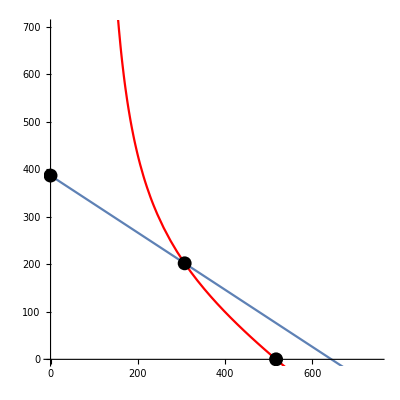

```mathematica
Show[p1,p2,Graphics[{PointSize[0.025],Point[{p1w,p1h}]}],Graphics[{PointSize[0.025],Point[{p2w,p2h}]}],Graphics[{PointSize[0.025],Point[{p3w,p3h}]}],PlotRange->{0,700},AspectRatio->1]
```

Jacobian evaluated at first fixed point: degenerate (also nonphysical)

```mathematica
j11=D[dhdt[H,W],H]/.fp1;
j12=D[dhdt[H,W],W]/.fp1;
j21=D[dwdt[H,W],H]/.fp1;
j22=D[dhdt[H,W],W]/.fp1;
J={{j11,j12},{j21,j22}};
Eigenvalues[J]
Eigenvectors[J];
```

{5.60768,0.}

Jacobian evaluated at second fixed point: stable node, not on the boundary

```mathematica
j11=D[dhdt[H,W],H]/.fp2;
j12=D[dhdt[H,W],W]/.fp2;
j21=D[dwdt[H,W],H]/.fp2;
j22=D[dhdt[H,W],W]/.fp2;
J={{j11,j12},{j21,j22}};
Eigenvalues[J]
Eigenvectors[J];
```

{-0.53013,-0.0933429}

Jacobian evaluated at third fixed point: unstable (what does one zero eigenvalue mean?), boundary point with H=0

```mathematica
j11=D[dhdt[H,W],H]/.fp3;
j12=D[dhdt[H,W],W]/.fp3;
j21=D[dwdt[H,W],H]/.fp3;
j22=D[dhdt[H,W],W]/.fp3;
J={{j11,j12},{j21,j22}};
Eigenvalues[J]
Eigenvectors[J];
```

{0.175652,0.}

Jacobian  evaluated at fourth fixed point: unstable (what does one zero eigenvalue mean?), boundary point with W=0

```mathematica
fp4={H->0, W->386.66667};
```

```mathematica
j11=D[dhdt[H,W],H]/.fp4;
j12=D[dhdt[H,W],W]/.fp4;
j21=D[dwdt[H,W],H]/.fp4;
j22=D[dhdt[H,W],W]/.fp4;
J={{j11,j12},{j21,j22}};
Eigenvalues[J]
Eigenvectors[J];
```

{0.446154,0.}